```mathematica
ABcounts={380,387,400,390,391,346,403,381,383,339,420,407,397,372,399,398}
```

{380,387,400,390,391,346,403,381,383,339,420,407,397,372,399,398}

```mathematica
ABcounts/20
```

{19,387/20,20,39/2,391/20,173/10,403/20,381/20,383/20,339/20,21,407/20,397/20,93/5,399/20,199/10}

```mathematica
Mean[%]
```

6193/320

```mathematica
N[6193/320]
```

19.3531

```mathematica
Length[ABcounts]
```

16

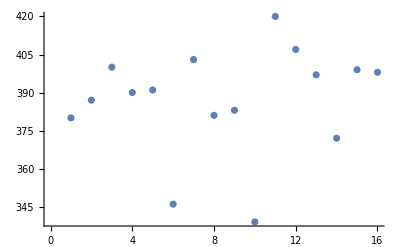

```mathematica
ListPlot[ABcounts]
```

```mathematica
Mean[ABcounts]//N
```

387.063

```mathematica
StandardDeviation[ABcounts]//N
```

20.9999

```mathematica
20.9999/20
```

1.05

```mathematica
StandardDeviation
```

StandardDeviation

```mathematica
Sqrt[387.063]/20
```

0.983696

```mathematica
ABTrate={{1000,3/380},{1050,6/387},{1100,2/400},{1150,1/390},{1200,6/334},{1250,7/391},{1300,23/346},{1350,47/403},{1400,75/381},{1450,253/1092},{1500,327/1254}}
```

{{1000,3/380},{1050,2/129},{1100,1/200},{1150,1/390},{1200,3/167},{1250,7/391},{1300,23/346},{1350,47/403},{1400,25/127},{1450,253/1092},{1500,109/418}}

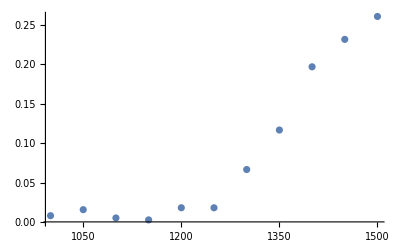

```mathematica
ListPlot[ABTrate]
```

```mathematica
ABTVrate={{1350,48/383},{1365,45/339},{1380,51/420},{1395,43/407},{1410,48/397},{1425,49/372},{1440,55/399},{1455,38/398},{1470,43/498},{1485,109/1111},{1500,111/1177}}
```

{{1350,48/383},{1365,15/113},{1380,17/140},{1395,43/407},{1410,48/397},{1425,49/372},{1440,55/399},{1455,19/199},{1470,43/498},{1485,109/1111},{1500,111/1177}}

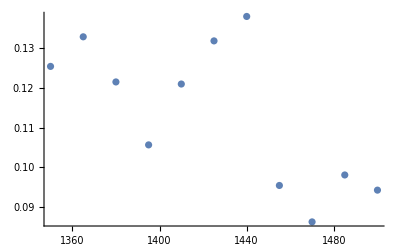

```mathematica
ListPlot[ABTVrate]
```

```mathematica
path="/Users/jackson/Muon-Lifetime/data/"
```

/Users/jackson/Muon-Lifetime/data/

```mathematica
data1=Import[StringJoin[path,"data1.csv"],"Data"];
```

```mathematica
data1=data1⟦23;;⟧;
```

```mathematica
data2=Import[StringJoin[path,"data2.csv"],"Data"];
```

```mathematica
data2=data2⟦23;;⟧;
```

```mathematica
data3=Import[StringJoin[path,"data3.csv"],"Data"];
```

```mathematica
data3=data3⟦23;;⟧;
```

```mathematica
data4=Import[StringJoin[path,"data4.csv"],"Data"];
```

```mathematica
data4=data4⟦23;;⟧;
```

```mathematica
data5=Import[StringJoin[path,"data5.csv"],"Data"];
```

```mathematica
data5=data5⟦23;;⟧;
```

```mathematica
dataTotal=Table[{data1⟦i⟧⟦1⟧,data1⟦i⟧⟦3⟧+data2⟦i⟧⟦3⟧+data3⟦i⟧⟦3⟧+data4⟦i⟧⟦3⟧+data5⟦i⟧⟦3⟧},{i,1,Length[data1]}];
```

```mathematica
dataTotal=dataTotal⟦11;;⟧;
```

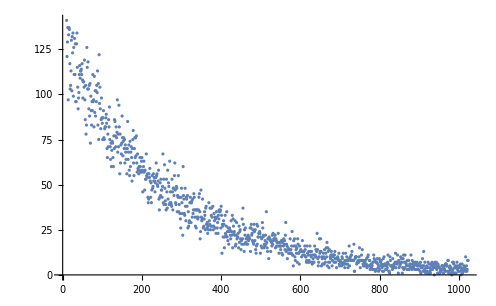

```mathematica
ListPlot[dataTotal]
```

```mathematica
fit=NonlinearModelFit[dataTotal,N0 E^(-t/τ),{N0,τ},t]
```

FittedModel[128.547 ⅇ^(-0.00385465 t)]

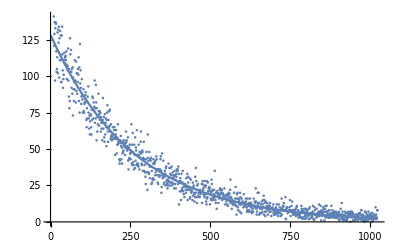

```mathematica
Show[ListPlot[dataTotal],Plot[fit[x],{x,1,1023}]]
```